```mathematica
(*DEFINE PARAMETERS*)
```

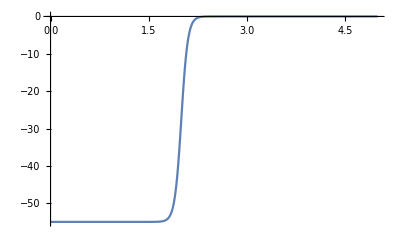

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=55;R=2;a=0.05;μ=8/9 Subscript[m, N];
rmax=5;dr=0.01;
rlist=Range[0,rmax,dr];
len=Length[rlist];
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*CALCULATE HAMILTONIAN MATRIX*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
k[En_]:=Sqrt[-(2μ En)/ℏc^2];
B[En_]:=-k[En] rmax;
Hnew[En_]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B[En]/rmax-1);H)
eigenv[{En_,i_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En]]],First];{eval[[i]],i})
```

```mathematica
(*CALCULATE EIGENSYSTEM*)
```

```mathematica
ϵ=10^-10;
n=1;
evals=List[];evecs=List[];
En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,10][[-1,1]];
While[Re[En]<0,
evals=Append[evals,En];
evecs=Append[evecs,evec[[n]]];n++;En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,10][[-1,1]];]
```

```mathematica
(*{eval,evec}={eval,evec}[[All,Position[{eval,evec}[[1,All]],_?(#<0&)][[All,1]]]];*)
(*En=NestWhileList[SetPrecision[eigenv,5]{-V0,1},UnsameQ,2,100]*)
(*FindRoot[eigenv[{x,1}][[1]]==x,{x,-V0/2,-V0,0},WorkingPrecision->2]*)
(*Plot[{eigenv[{x,n}][[1]],#&[x]},{x,-V0,0}]*)
```

```mathematica
(*MATCH AMPLITUDE & PLOT RESULTS*)
```

```mathematica
wave[En_,r_]:=Exp[-k[En] r];
const[i_]:=evecs[[i,-1]]/wave[evals[[i]],rmax];
rmaxx=10.;
Manipulate[ListLinePlot[{Transpose[{rlist,evecs⟦i⟧}],Transpose[{Range[rmax,rmaxx,dr],const[i] wave[evals[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All],{i,1,Length[evals],1}]
```